4/(3 (-1+ⅇ^(√(2/3) phi))^2)

-(4 (-2+ⅇ^(√(2/3) phi)))/(3 (-1+ⅇ^(√(2/3) phi))^2)

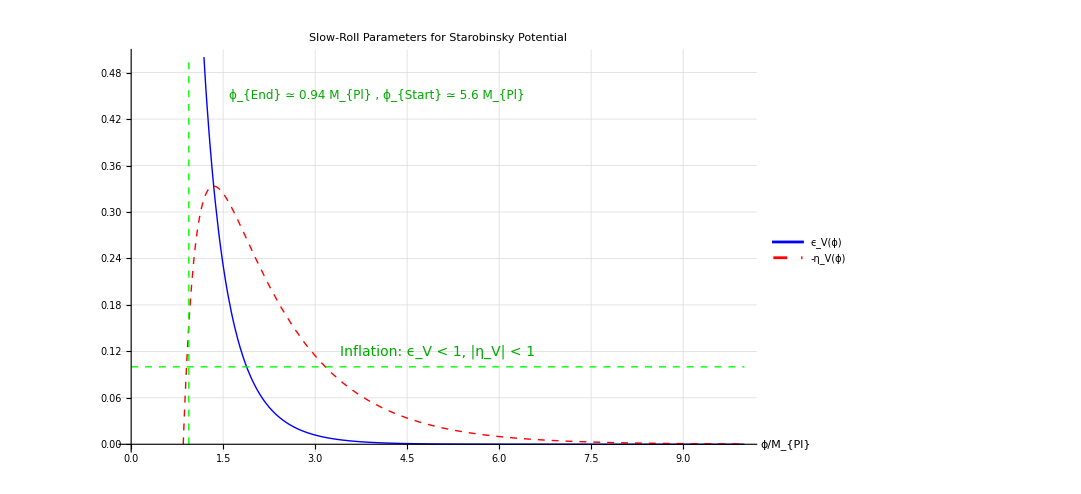

```mathematica
MPl=1;
M=1;
V[phi_]:=(3 MPl^2 M^2)/4 (1-Exp[-Sqrt[2/3] phi/MPl])^2

Vp[phi_]:=D[V[phi],phi]

Vpp[phi_]:=D[V[phi],{phi,2}]

epsilonV[phi_]:=(MPl^2/2) (Vp[phi]/V[phi])^2
etaV[phi_]:=MPl^2 (Vpp[phi]/V[phi])
epsilonV[phi_]=Simplify[(MPl^2/2) (Vp[phi]/V[phi])^2]
etaV[phi_]=Simplify[MPl^2 (Vpp[phi]/V[phi])]
Plot[{epsilonV[phi],-etaV[phi]},{phi,0,10},PlotStyle->{{Thick,Blue},{Thick,Red,Dashed}},AxesLabel->{"ϕ/M_{Pl}"},PlotLabel->Style["Slow-Roll Parameters for Starobinsky Potential",16],GridLines->Automatic,ImageSize->800,PlotRange->{0,0.5},PlotLegends->Placed[{"ϵ_V(ϕ)","-η_V(ϕ)"},{0.8,0.8}],Epilog->{{Dashed,Green,Thick,Line[{{0,0.1},{10,0.1}}]},Text[Style["Inflation: \!\(\*SubscriptBox[\(ϵ\), \(V\)]\) < 1, |\!\(\*SubscriptBox[\(η\), \(V\)]\)| < 1",Darker[Green],14],{5,0.12}],{Dashed,Green,Line[{{0.94,0},{0.94,0.5}}]},Text[Style["ϕ_{End} ≃ 0.94 M_{Pl} , ϕ_{Start} ≃ 5.6 M_{Pl}",Darker[Green],12],{4,0.45}]}]
```